## EdgesOnBounary-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51a (07 June 2017)) loaded Wed 7 Jun 2017 16:32:52
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

Generate a random template constrained to  circle

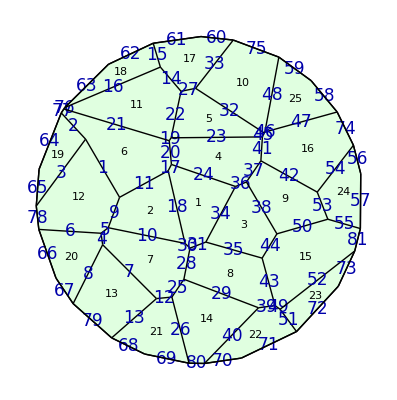

```mathematica
w=TemplateRandomCircularGrid[25,100];
ShowTissue[w, "CellNumbers"-> True, "EdgeNumbers"-> True, "EdgeNumberStyle"-> {Darker[Blue], FontSize-> 17,Background-> Pink}]
```

```mathematica
EdgesOnBoundary[w]
```

{56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81}

```mathematica
EdgesNotOnBoundary[w]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55}